# Enostavna uporaba funkcije Manipulate

## Naloga 1

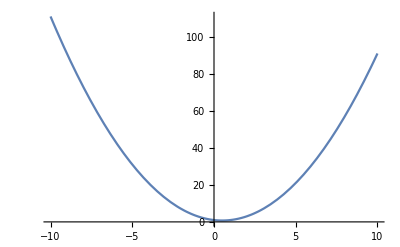

```mathematica
a=1;b=-1;c=1;
Plot[a x^2+b x+c,{x, -10,10}] (*najprej narediš plot, da vidiš če dela*)
Manipulate[
Plot[a x^2+b x+c,{x, -10,10}],
{a,-10,10},
{b,-10,10},
{c,-10,10}
]
```

```mathematica
ClearAll[a,b,c]
Manipulate[
Plot[a Sin[b x+c],{x, -3,3}],
{a, -3,3},
{b, -3,3},
{c, -3,3}
]
```

```mathematica
ClearAll[a,b,c]
Manipulate[
Plot[Sin[a x]+Sin[b],{x, 1,20}],
{a, 1,20},
{b,1,20}
]
```

## Naloga 2

```mathematica
Manipulate[Expand[(x+y)^n],{n,1,20,1}]
```

```mathematica
Manipulate[TrigExpand[Sin[n x]],{n,1,20,1}]
```

```mathematica
Manipulate[Table[x^2,{x,1,n}],
{n,1,20,1}
]
```

```mathematica
Manipulate[Table[Sin[x Pi/2],{x,1,n}],
{n,1,20,1}
]
```

## Met žogice

```mathematica
(*neki ne dela...uni v0 je čuden*)
```

```mathematica
g={0,-9.81};
v = {15,10};
V[v_,t_]:=v+g t
X[t_]:={0,10}+V[v,t]t+g t^2/2

Slika[v_,t_]:=Graphics[{
PointSize[0.1],
Point[{X[t]}]
},
Axes->True,
PlotRange->{{-1,25},{-5,15}},
AspectRatio->1
]

Manipulate[
Slika[v0,t],
{t,0,5},
{v0,{15,10},{0,0},{20,20}}
]
```